```mathematica
setpositenv[{n_Integer/;n≥2,e_Integer/;e≥0}]:=
({nbits, es} = {n,e};
npat=2^nbits;
useed=2^(2^es);
{minpos, maxpos}={useed^(-nbits+2), useed^(nbits-2)};
qsize=2^(Ceiling[Log[2,(nbits-2)*2^(es+2)+5]]);
qextra=qsize-(nbits-2)*2^(es+2);)
```

```mathematica
(*Test - OK*)
setpositenv[{6,1}]
{nbits,es,npat,useed,minpos,maxpos,qsize,qextra}
```

{6,1,64,4,1/256,256,64,32}

```mathematica
(*Extracting the sign bit*)
positQ[p_Integer]:=0≤p<npat
twoscomp[sign_,p_]:=Mod[If[sign>0,p,npat-p],npat]
signbit[p_/;positQ[p]]:=IntegerDigits[p,2,nbits][[1]]
```

```mathematica
(*Test - OK*)
signbit[1]
signbit[npat-1]
signbit[npat]
```

0

1

signbit[64]

```mathematica
(*Extracting the regime bits*)
regimebits[p_/;positQ[p]]:=Module[{q=twoscomp[1-signbit[p],p],bits,bit2,npower,tempbits},bits=IntegerDigits[q,2,nbits];
bit2=bits[[2]];(*Look for the run length after the sign bit.*)tempbits=Join[Drop[bits,1],{1-bit2}];(*Drop the sign bit,but append a complement bit as a sure-fire way to end the run.*)npower=(Position[tempbits,1-bit2,1,1])⟦1⟧-1;
(*Find first opposite bit.*)Take[bits,{2,Min[npower+1,nbits]}]]
regimevalue[bits_]:=If[bits[[1]]==1,Length[bits]-1,-Length[bits]]
```

```mathematica
(*Test - OK*)
regimebits[2^^000011]
regimevalue[%]
```

{0,0,0}

-3

```mathematica
regimebits[2^^100001]
regimevalue[%]
```

{1,1,1,1,1}

4

```mathematica
(*Extracting the exponent bits*)
exponentbits[p_/;positQ[p]]:=Module[{q=twoscomp[1-signbit[p],p],bits,startbit},startbit=Length[regimebits[q]]+3;
bits=IntegerDigits[q,2,nbits];
If[startbit>nbits,{},Take[bits,{startbit,Min[startbit+es-1,nbits]}]]]
```

```mathematica
(*Extracting the fraction bits*)
fractionbits[p_/;positQ[p]]:=Module[{q=twoscomp[1-signbit[p],p],bits,startbit},startbit=Length[regimebits[q]]+3+es;
bits=IntegerDigits[q,2,nbits];
If[startbit>nbits,{},Take[bits,{startbit,nbits}]]]
```

```mathematica
colorcodep[p_/;positQ[p]]:=Module[{s=signbit[p],r=regimebits[p],e=exponentbits[p],f=fractionbits[p]},Row[{IntegerString[p,2,nbits],"→",Style[If[s ==0,"+","-"], Red],Style[Row[r],RGBColor[0.8549019607843137, 0.6470588235294118, 0.12549019607843137] ],If[Length[r]≤nbits-2,Style[1-r[[1]] , Brown],""],If[Length[e]>0,Style[Row[e], RGBColor[0.2549019607843137, 0.4117647058823529, 0.8823529411764706]],""],If[Length[f]>0,Row[f],""]}]]
```

```mathematica
(*The p2x function*)
p2x[p_/;positQ[p]]:=
Module[{s=(-1)^(signbit[p]), k=regimevalue[regimebits[p]], e=exponentbits[p], f=fractionbits[p]},
e=Join[e, Table[0,es-Length[e]]];
(* Pad with 0s on the right of they are clipped off. *)
e=FromDigits[e,2];
If[f=={},f=1,f=1+FromDigits[f,2]*2^(-Length[f])];
Which[
p==0,0,
p==npat/2,ComplexInfinity, (* The two exception values, 0 and +-Infinity *) True, s*useed^k*2^e*f]]
```

```mathematica
(*Test - OK*)
setpositenv[{6,2}];
Table[Row[{colorcodep[u+j],"  ",p2x[u+j],"    "}],
{u,0,31},{j,32,0,-32}]//TableForm
```

100000→-00000  ComplexInfinity     | 000000→+00000  0    
100001→-11111  -65536     | 000001→+00001  1/65536    
100010→-11110  -4096     | 000010→+00010  1/4096    
100011→-11101  -1024     | 000011→+00011  1/1024    
100100→-11100  -256     | 000100→+00100  1/256    
100101→-11011  -128     | 000101→+00101  1/128    
100110→-11010  -64     | 000110→+00110  1/64    
100111→-11001  -32     | 000111→+00111  1/32    
101000→-11000  -16     | 001000→+01000  1/16    
101001→-10111  -12     | 001001→+01001  3/32    
101010→-10110  -8     | 001010→+01010  1/8    
101011→-10101  -6     | 001011→+01011  3/16    
101100→-10100  -4     | 001100→+01100  1/4    
101101→-10011  -3     | 001101→+01101  3/8    
101110→-10010  -2     | 001110→+01110  1/2    
101111→-10001  -3/2     | 001111→+01111  3/4    
110000→-10000  -1     | 010000→+10000  1    
110001→-01111  -3/4     | 010001→+10001  3/2    
110010→-01110  -1/2     | 010010→+10010  2    
110011→-01101  -3/8     | 010011→+10011  3    
110100→-01100  -1/4     | 010100→+10100  4    
110101→-01011  -3/16     | 010101→+10101  6    
110110→-01010  -1/8     | 010110→+10110  8    
110111→-01001  -3/32     | 010111→+10111  12    
111000→-01000  -1/16     | 011000→+11000  16    
111001→-00111  -1/32     | 011001→+11001  32    
111010→-00110  -1/64     | 011010→+11010  64    
111011→-00101  -1/128     | 011011→+11011  128    
111100→-00100  -1/256     | 011100→+11100  256    
111101→-00011  -1/1024     | 011101→+11101  1024    
111110→-00010  -1/4096     | 011110→+11110  4096    
111111→-00001  -1/65536     | 011111→+11111  65536

```mathematica
(* Converting values into posits *)
(* Building the x2p conversion function *)
positableQ[x_]:=(Abs[x] == ∞ || x∈Reals)
x2p[x_/;positableQ[x]]:=Module[{i,p,e=2^(es-1),y=Abs[x]},Which[(*First,take care of the two exception values:*)y == 0,0,(*all 0 bits s*)y == ∞,BitShiftLeft[1,nbits-1],(*1 followed by all 0 bits*)True,If[y≥1,(*Northeast quadrant:*)p=1;
i=2;(*Shift in 1s from the right and scale down.*)While[y≥useed&&i<nbits,{p,y,i}={2 p+1,y/useed,i+1}];
p=2 p;i++,(*Else,southeast quadrant:*)p=0;
i=1;(*Shift in 0s from the right and scale up.*)While[y<1&&i≤nbits,{y,i}={y*useed,i+1}];
If[i≥nbits,p=2;
i=nbits+1,p=1;
i++]];
(*Extract exponent bits:*)While[e>1/2&&i≤nbits,p=2 p;
If[y≥2^e,y/=2^e;
p++];
e/=2;i++];
y--;(*Fraction bits;subtract the hidden bit*)While[y>0&&i≤nbits,y=2 y;p=2 p+Floor[y];y-=Floor[y];i++];
p*=2^(nbits+1-i);
i++;
(*Round to nearest;tie goes to even*)i=BitAnd[p,1];p=Floor[p/2];
p=Which[i == 0,p,(*closer to lower value*)y == 1||y == 0,p+BitAnd[p,1],(*tie goes to nearest even*)True,p+1 (*closer to upper value*)];
Mod[If[x<0,npat-p,p],npat (*Simulate 2's complement*)]]]
```

```mathematica
OverBar[x_]:=p2x[x2p[x]];
SetAttributes[OverBar,Listable]
```

```mathematica
setpositenv[{10,1}]
OverBar[Pi]
N[%]
```

101/32

3.15625

```mathematica
setpositenv[{8,1}]
OverBar[{minpos,maxpos}]
```

{1/4096,4096}

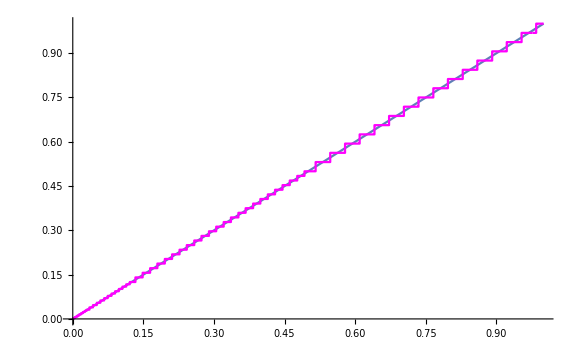

```mathematica
setpositenv[{8,1}]
p1:=Plot[x,{x,0,1.0}]
p2:=ListStepPlot[Table[{x,OverBar[x]}, {x, 0, 1, minpos}], PlotStyle->Magenta]
Show[{p1,p2},ImageSize->Large]
```

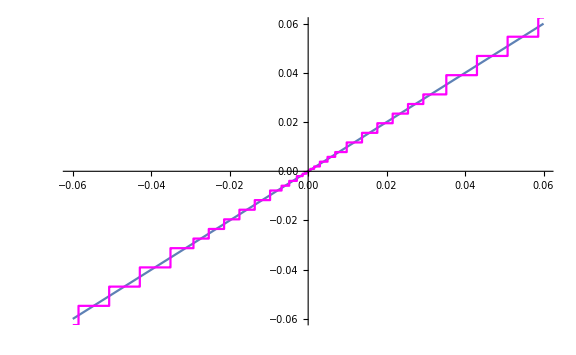

```mathematica
p11:=Plot[x,{x,-0.06,0.06}]
p12:=ListStepPlot[Table[{x,OverBar[x]}, {x, -0.06,0.06, minpos}], PlotStyle->Magenta]
Show[p11,p12,ImageSize->Large]
```

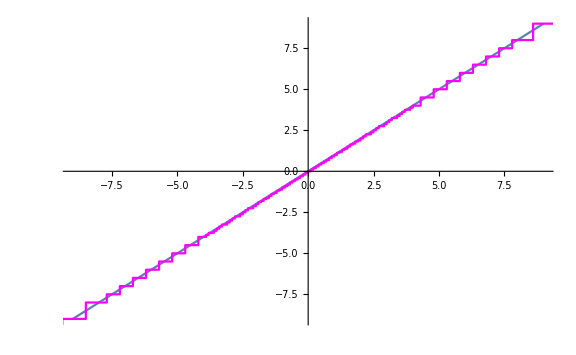

```mathematica
p11:=Plot[x,{x,-9,9}]
p12:=ListStepPlot[Table[{x,OverBar[x]}, {x, -maxpos,maxpos, 0.1}], PlotStyle->Magenta]
Show[p11,p12,ImageSize->Large]
```

```mathematica
(* Creating an IEEE 754 float environment *)
setfloatenv[{n_Integer/;n≥4,e_Integer/;e≥2}]:=({nfbits,esize,fsize}={n,e,n-e-1};
bias=2^(esize-1)-1;
smallsubnormal=2^(1-bias-fsize);
smallnormal=2^(1-bias);
maxfloat=2^(bias)*( 1+(2^(fsize)-1)/(2^(fsize)));
minroundable=smallsubnormal/2;
maxroundable=2^(bias )*( 1+(2^(fsize)-1/2)/(2^(fsize)));)
```

```mathematica
(* Test - OK *)
setfloatenv[{6,2}]
{nfbits,esize,fsize,bias,smallsubnormal,smallnormal,maxfloat,minroundable,maxroundable}
```

{6,2,3,1,1/8,1,15/4,1/16,31/8}

```mathematica
(* The function that converts a float to its numerical value:f2x *)
f2x [f_Integer/;0≤f<2^nfbits]:=
Module[{emask=FromDigits[Table[1,esize],2],
exp,fmask=FromDigits[Table[1,fsize],2],
frac,sgn,smask=BitShiftLeft[1,nfbits-1]},sgn=BitShiftRight[BitAnd[smask,f],nfbits-1];
exp=BitAnd[BitShiftRight[f,fsize],emask];
frac=BitAnd[fmask,f];
Which[
exp==emask,If[frac==0,(-1)^sgn×∞,Indeterminate],
exp==0,(-1)^sgn×2^(1-bias)×(frac / (2^fsize)),
True,(-1)^sgn×2^(exp-bias)×(1+frac /( 2^fsize))]]
```

```mathematica
(* Converting numbers into floats *)
floatableQ[x_]:=(x===Indeterminate∨x===∞∨x===-∞∨x∈Reals)
x2f[x_/;floatableQ[x]]:=Module[{e=0,f,sgn,y},
Which[
x===Indeterminate||¬floatableQ[x],
FromDigits[Table[1,nfbits],2],(*NaN exceptions*)
y=Abs[x];
sgn=BitShiftLeft[Boole[x<0],nfbits-1];
y==0,0,(*Zero exception*)
y≥maxroundable,BitOr[sgn,BitShiftLeft[FromDigits[Table[1,esize],2],fsize]],(*Infinity and overflow exceptions*)
y<smallnormal,BitOr[sgn,Round[y/smallsubnormal]],
(*subnormal exceptions*)
True,(*Else x is normal.Find the exponent and fraction fields.*)(*At most one of the next two While loops will execute.*)
While[y≥2,y/=2;e++];
While[y<1,y*=2;e--];
(*We now have 1≤y<2.*)
f=Round[(y-1)*2^fsize];
(*This may round up to 2,so we add f,instead of ORing it.*)
BitOr[sgn,BitShiftLeft[bias+e,fsize]]+f]]
colorcodef[f_/;floatableQ[f]]:=
Module[{fbits=IntegerDigits[f,2,nfbits]},Row[{Style[fbits[[1]], Red],"",Style[Row[Take[fbits,{2,esize+1}]],Blue],"",Row[Take[fbits,-nfbits+esize+1]]}]]
```

```mathematica
(* Test - OK*)
colorcodef[2^^001101]
N[f2x[2^^001101]]
```

001101

1.625

```mathematica
(* Restriction to a float vocabulary:the underbar operator *)
UnderBar[x_]:=f2x[x2f[x]]
SetAttributes[UnderBar,Listable]
```

```mathematica
(* Test - OK *)
UnderBar[Pi]
N[%]
```

13/4

3.25

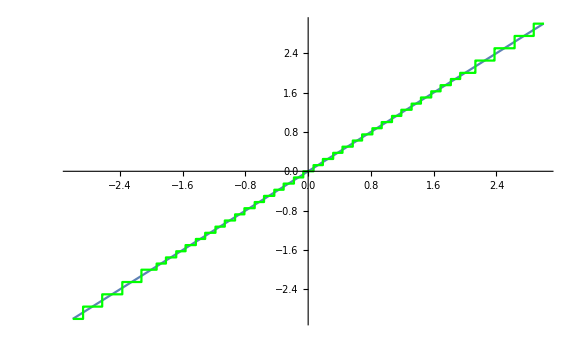

```mathematica
(* Let’s do two quick graphics tests like the ones done for posits *)
setfloatenv[{6,2}]
f1:=Plot[x,{x,-3,3}]
f2:=ListStepPlot[Table[{x,UnderBar[x]}, {x, -3,3, minroundable/10}], PlotStyle->Green]
Show[{f1,f2},ImageSize->Large]
```

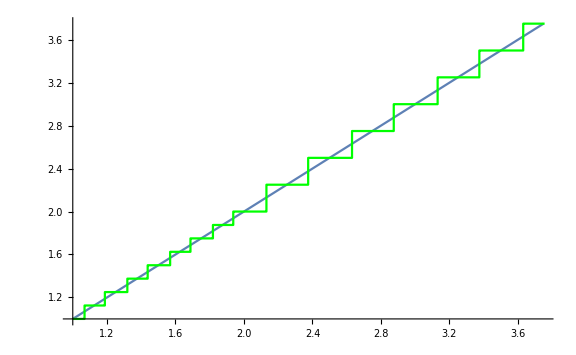

```mathematica
f11:=Plot[x,{x,1,maxfloat}]
f22:=ListStepPlot[Table[{x,UnderBar[x]}, {x, 1,maxfloat, minroundable/10}], PlotStyle->Green]
Show[{f11,f22},ImageSize->Large]
```

```mathematica
(* 6 Floats vs.Posits Preview:Accuracy on a 32-bit budget *)
```

```mathematica
(* 7 Posits versus IEEE-type Floats:A Metric-Based Study *)
```

```mathematica
floatfix[i_Integer]:=If[i<2^(nfbits-1),2^(nfbits)-i-1,i-2^(nfbits-1)]
positfix[i_Integer]:=If[i<npat/2,i+npat/2,i-npat/2]
```

```mathematica
setfloatenv[{8,4}]
float8=Table[f2x[floatfix[f]],{f,0,2^(nfbits)-1}];
Table[TableForm[{float8[[i]]}],{i,1,Length[float8]}]
```

{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,-∞,-240,-224,-208,-192,-176,-160,-144,-128,-120,-112,-104,-96,-88,-80,-72,-64,-60,-56,-52,-48,-44,-40,-36,-32,-30,-28,-26,-24,-22,-20,-18,-16,-15,-14,-13,-12,-11,-10,-9,-8,-15/2,-7,-13/2,-6,-11/2,-5,-9/2,-4,-15/4,-7/2,-13/4,-3,-11/4,-5/2,-9/4,-2,-15/8,-7/4,-13/8,-3/2,-11/8,-5/4,-9/8,-1,-15/16,-7/8,-13/16,-3/4,-11/16,-5/8,-9/16,-1/2,-15/32,-7/16,-13/32,-3/8,-11/32,-5/16,-9/32,-1/4,-15/64,-7/32,-13/64,-3/16,-11/64,-5/32,-9/64,-1/8,-15/128,-7/64,-13/128,-3/32,-11/128,-5/64,-9/128,-1/16,-15/256,-7/128,-13/256,-3/64,-11/256,-5/128,-9/256,-1/32,-15/512,-7/256,-13/512,-3/128,-11/512,-5/256,-9/512,-1/64,-7/512,-3/256,-5/512,-1/128,-3/512,-1/256,-1/512,0,0,1/512,1/256,3/512,1/128,5/512,3/256,7/512,1/64,9/512,5/256,11/512,3/128,13/512,7/256,15/512,1/32,9/256,5/128,11/256,3/64,13/256,7/128,15/256,1/16,9/128,5/64,11/128,3/32,13/128,7/64,15/128,1/8,9/64,5/32,11/64,3/16,13/64,7/32,15/64,1/4,9/32,5/16,11/32,3/8,13/32,7/16,15/32,1/2,9/16,5/8,11/16,3/4,13/16,7/8,15/16,1,9/8,5/4,11/8,3/2,13/8,7/4,15/8,2,9/4,5/2,11/4,3,13/4,7/2,15/4,4,9/2,5,11/2,6,13/2,7,15/2,8,9,10,11,12,13,14,15,16,18,20,22,24,26,28,30,32,36,40,44,48,52,56,60,64,72,80,88,96,104,112,120,128,144,160,176,192,208,224,240,∞,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}

```mathematica
posit8=Table[p2x[positfix[j]],{j,0,npat-1}];
Table[TableForm[{posit8[[i]]}],{i,1,npat}]
```

{ComplexInfinity,-4096,-1024,-512,-256,-192,-128,-96,-64,-56,-48,-40,-32,-28,-24,-20,-16,-15,-14,-13,-12,-11,-10,-9,-8,-15/2,-7,-13/2,-6,-11/2,-5,-9/2,-4,-31/8,-15/4,-29/8,-7/2,-27/8,-13/4,-25/8,-3,-23/8,-11/4,-21/8,-5/2,-19/8,-9/4,-17/8,-2,-31/16,-15/8,-29/16,-7/4,-27/16,-13/8,-25/16,-3/2,-23/16,-11/8,-21/16,-5/4,-19/16,-9/8,-17/16,-1,-31/32,-15/16,-29/32,-7/8,-27/32,-13/16,-25/32,-3/4,-23/32,-11/16,-21/32,-5/8,-19/32,-9/16,-17/32,-1/2,-31/64,-15/32,-29/64,-7/16,-27/64,-13/32,-25/64,-3/8,-23/64,-11/32,-21/64,-5/16,-19/64,-9/32,-17/64,-1/4,-15/64,-7/32,-13/64,-3/16,-11/64,-5/32,-9/64,-1/8,-15/128,-7/64,-13/128,-3/32,-11/128,-5/64,-9/128,-1/16,-7/128,-3/64,-5/128,-1/32,-7/256,-3/128,-5/256,-1/64,-3/256,-1/128,-3/512,-1/256,-1/512,-1/1024,-1/4096,0,1/4096,1/1024,1/512,1/256,3/512,1/128,3/256,1/64,5/256,3/128,7/256,1/32,5/128,3/64,7/128,1/16,9/128,5/64,11/128,3/32,13/128,7/64,15/128,1/8,9/64,5/32,11/64,3/16,13/64,7/32,15/64,1/4,17/64,9/32,19/64,5/16,21/64,11/32,23/64,3/8,25/64,13/32,27/64,7/16,29/64,15/32,31/64,1/2,17/32,9/16,19/32,5/8,21/32,11/16,23/32,3/4,25/32,13/16,27/32,7/8,29/32,15/16,31/32,1,17/16,9/8,19/16,5/4,21/16,11/8,23/16,3/2,25/16,13/8,27/16,7/4,29/16,15/8,31/16,2,17/8,9/4,19/8,5/2,21/8,11/4,23/8,3,25/8,13/4,27/8,7/2,29/8,15/4,31/8,4,9/2,5,11/2,6,13/2,7,15/2,8,9,10,11,12,13,14,15,16,20,24,28,32,40,48,56,64,96,128,192,256,512,1024,4096}

```mathematica
float8
invf:=1/float8
```

{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,-∞,-240,-224,-208,-192,-176,-160,-144,-128,-120,-112,-104,-96,-88,-80,-72,-64,-60,-56,-52,-48,-44,-40,-36,-32,-30,-28,-26,-24,-22,-20,-18,-16,-15,-14,-13,-12,-11,-10,-9,-8,-15/2,-7,-13/2,-6,-11/2,-5,-9/2,-4,-15/4,-7/2,-13/4,-3,-11/4,-5/2,-9/4,-2,-15/8,-7/4,-13/8,-3/2,-11/8,-5/4,-9/8,-1,-15/16,-7/8,-13/16,-3/4,-11/16,-5/8,-9/16,-1/2,-15/32,-7/16,-13/32,-3/8,-11/32,-5/16,-9/32,-1/4,-15/64,-7/32,-13/64,-3/16,-11/64,-5/32,-9/64,-1/8,-15/128,-7/64,-13/128,-3/32,-11/128,-5/64,-9/128,-1/16,-15/256,-7/128,-13/256,-3/64,-11/256,-5/128,-9/256,-1/32,-15/512,-7/256,-13/512,-3/128,-11/512,-5/256,-9/512,-1/64,-7/512,-3/256,-5/512,-1/128,-3/512,-1/256,-1/512,0,0,1/512,1/256,3/512,1/128,5/512,3/256,7/512,1/64,9/512,5/256,11/512,3/128,13/512,7/256,15/512,1/32,9/256,5/128,11/256,3/64,13/256,7/128,15/256,1/16,9/128,5/64,11/128,3/32,13/128,7/64,15/128,1/8,9/64,5/32,11/64,3/16,13/64,7/32,15/64,1/4,9/32,5/16,11/32,3/8,13/32,7/16,15/32,1/2,9/16,5/8,11/16,3/4,13/16,7/8,15/16,1,9/8,5/4,11/8,3/2,13/8,7/4,15/8,2,9/4,5/2,11/4,3,13/4,7/2,15/4,4,9/2,5,11/2,6,13/2,7,15/2,8,9,10,11,12,13,14,15,16,18,20,22,24,26,28,30,32,36,40,44,48,52,56,60,64,72,80,88,96,104,112,120,128,144,160,176,192,208,224,240,∞,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}

```mathematica
Mean[(MemberQ[posit8,#1]&)/@(1/posit8)]
```

Power::infy: Infinite expression 1/0 encountered.

1/256 (208 False+48 True)

```mathematica
N[48/256]
```

0.1875

```mathematica
Length[float8]
```

256

```mathematica
invf
```

Power::infy: Infinite expression 1/0 encountered.

{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,0,-1/240,-1/224,-1/208,-1/192,-1/176,-1/160,-1/144,-1/128,-1/120,-1/112,-1/104,-1/96,-1/88,-1/80,-1/72,-1/64,-1/60,-1/56,-1/52,-1/48,-1/44,-1/40,-1/36,-1/32,-1/30,-1/28,-1/26,-1/24,-1/22,-1/20,-1/18,-1/16,-1/15,-1/14,-1/13,-1/12,-1/11,-1/10,-1/9,-1/8,-2/15,-1/7,-2/13,-1/6,-2/11,-1/5,-2/9,-1/4,-4/15,-2/7,-4/13,-1/3,-4/11,-2/5,-4/9,-1/2,-8/15,-4/7,-8/13,-2/3,-8/11,-4/5,-8/9,-1,-16/15,-8/7,-16/13,-4/3,-16/11,-8/5,-16/9,-2,-32/15,-16/7,-32/13,-8/3,-32/11,-16/5,-32/9,-4,-64/15,-32/7,-64/13,-16/3,-64/11,-32/5,-64/9,-8,-128/15,-64/7,-128/13,-32/3,-128/11,-64/5,-128/9,-16,-256/15,-128/7,-256/13,-64/3,-256/11,-128/5,-256/9,-32,-512/15,-256/7,-512/13,-128/3,-512/11,-256/5,-512/9,-64,-512/7,-256/3,-512/5,-128,-512/3,-256,-512,ComplexInfinity,ComplexInfinity,512,256,512/3,128,512/5,256/3,512/7,64,512/9,256/5,512/11,128/3,512/13,256/7,512/15,32,256/9,128/5,256/11,64/3,256/13,128/7,256/15,16,128/9,64/5,128/11,32/3,128/13,64/7,128/15,8,64/9,32/5,64/11,16/3,64/13,32/7,64/15,4,32/9,16/5,32/11,8/3,32/13,16/7,32/15,2,16/9,8/5,16/11,4/3,16/13,8/7,16/15,1,8/9,4/5,8/11,2/3,8/13,4/7,8/15,1/2,4/9,2/5,4/11,1/3,4/13,2/7,4/15,1/4,2/9,1/5,2/11,1/6,2/13,1/7,2/15,1/8,1/9,1/10,1/11,1/12,1/13,1/14,1/15,1/16,1/18,1/20,1/22,1/24,1/26,1/28,1/30,1/32,1/36,1/40,1/44,1/48,1/52,1/56,1/60,1/64,1/72,1/80,1/88,1/96,1/104,1/112,1/120,1/128,1/144,1/160,1/176,1/192,1/208,1/224,1/240,0,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}

```mathematica
N[256*0.13]
```

33.28

```mathematica
34+2+14-256
```

-206